```mathematica
Clear["GLobals`*"]
```

----- Creamos una funcion ------
 Module [ { Inicializamos los valores separados por comas } , Funcion [ ] : = Escribimos la funcion ]

```mathematica
Module[{a=314159269,c=453806245,m=2^31,z=1000},RndData[]:= (z=Mod[z*a+c,m])/m //N
]
```

```mathematica
RndData[]
```

0.50313

----- Recogemos muestras -----

```mathematica
muestras =Table[RndData[],20];
```

```mathematica
muestras[[1;;20]]
```

{0.607222,0.243107,0.292092,0.411891,0.145711,0.126371,0.513474,0.0849767,0.498178,0.408791,0.383209,0.169938,0.832972,0.0415893,0.534402,0.599613,0.734372,0.323467,0.528235,0.408409}

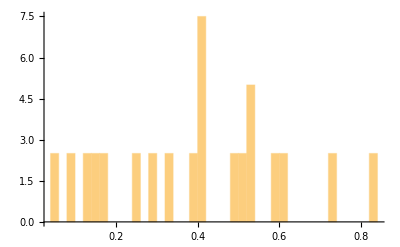

```mathematica
Histogram[muestras,30,PDF]
```

Creamos la funcion exponencial

```mathematica
RndExp[rate_]:=-Log[RndData[]]/rate;
```

```mathematica
muestras2=Table[RndExp[100],10000];
muestras2[[1;;20]]
```

{0.00942944,0.0143801,0.000783458,0.00111721,0.00203192,0.00588782,0.056853,0.0235148,0.000247816,0.000755469,0.0147278,0.0301964,0.0217601,0.00385404,0.0289581,0.00218271,0.0174941,0.006262,0.018508,0.00426369}

```mathematica
g1=Plot[100*E^(-100*t),{t,0,0.042}]
```

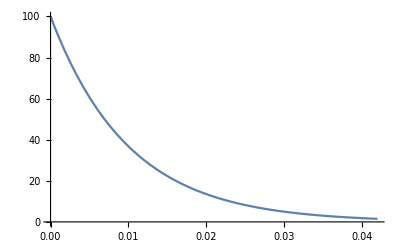

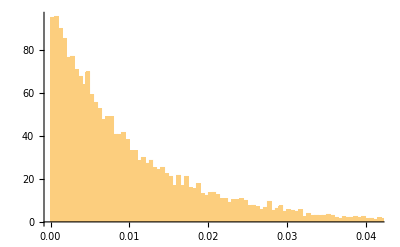

```mathematica
h1=Histogram[muestras2,200,PDF]
```

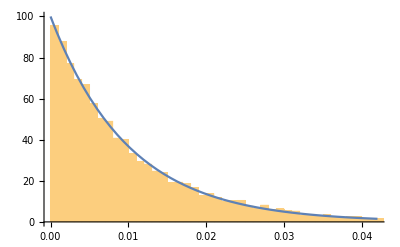

```mathematica
Show [h1,g1]
```

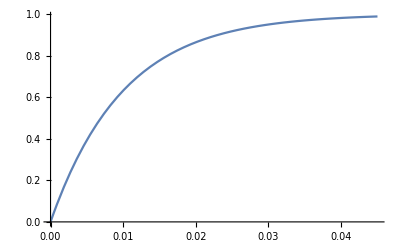

```mathematica
g=Plot[1-E^(-100*t),{t,0,0.045}]
```

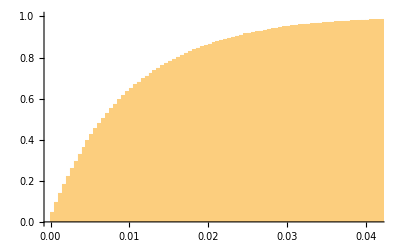

```mathematica
h=Histogram[muestras2,200,CDF]
```

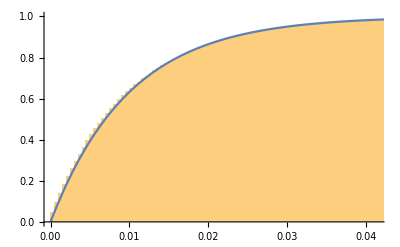

```mathematica
Show[h,g]
```